```mathematica
<<ACPackages`
<<ACPackages`Master`
```

```mathematica
SetWorkDir["2010.10.30\\chi09"]
```

d:\home\Anton\programs\tormagn-full\2010.10.30\chi09

```mathematica
SetWorkDir[]
```

d:\home\Anton\programs\tormagn

```mathematica
SetWorkDir["Debug"]
```

d:\home\Anton\programs\tormagn-full\Debug

```mathematica
SetWorkDir["2010.08.31\\chi13"]
```

d:\home\Anton\programs\tormagn-full\2010.08.31\chi13

```mathematica
$HistoryLength=1;
```

```mathematica
text=Import["mess0.log","Text"];StringLength[text]
```

996354

```mathematica
StringCases[text,RegularExpression["mB from\\s*(\\d+)\\s+"]:>ToExpression["$1"]]//Tally
```

{{197,3525},{325,3525},{317,3525},{189,3524}}

#### Разбор логов

```mathematica
text=Import["message.dat","Text"];
```

```mathematica
StrMsg[msg_String]:="(?s)(message of proc#(\\d+) at )?t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>msg
StrChg[par_String]:=StrMsg[par<>" was changed to"]
```

```mathematica
StrChg[par_String]:="t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>par<>" was changed to";
```

```mathematica
Rmt=StringCases[text,RegularExpression[StrChg["Rm"]]:>ToExpression["$3"]];
```

```mathematica
StringCases[text,RegularExpression[StrMsg["(.*?)"]]:>"$0"]//Length
```

215

```mathematica
StringCases[text,RegularExpression[StrChg["rc"]]:>"$3"]
```

{}

```mathematica
cs=StringCases[text,RegularExpression[StringJoin["(?s)(",StrChg["rc"],")?(.+?)(?=(",StrChg["rc"],")|$)"]]:>"$0"];cs={StringCases[#,RegularExpression[StrChg["rc"]]->"$3"],StringCases[#,RegularExpression[StrChg["Rm"]]->"$3"],StringCases[#,RegularExpression[StrMsg["snap is done"]]->"$5"]}&/@cs;
TableForm[{#⟦1⟧,#⟦2,-1⟧,#⟦3,-1⟧}&/@cs]
```

| 26.0000 | 40792
0.4750 | 26.0000 | 42214
0.5000 | 26.0000 | 43410
0.5250 | 26.0000 | 44425
0.5500 | 26.0000 | 45582

```mathematica
cs[[3]]
```

{{0.8091},{},{614,1140,1661,2186,2707,3233,3758,4284,4812,5332,5856,6382,6906,7428,7951,8475,9003,9523,10049,10576,11094,11621,12148,12671,13198,13721,14242,14766,15288,15818,16347,16866,17388,17912,18439,18965,19490,20012,20535,21060,21584,22106,22632,23155,23679,24203,24727,25253,25778,26296,26819,27345,27865,28386,28906,29430,29952,30472,30998,31521}}

```mathematica
ListPlot[ToExpression/@cs[[2,2]]]
```

```mathematica
fins=StringCases[text,RegularExpression["t=(15(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=(\\d+(\\.\\d+)?) sec:\nsnap is done"]:>{"$1","$3","$4"}]
```

{{15.0001,10199,1975.96},{15.0005,10564,1591.42},{15.0007,10866,581.238},{15.0010,11178,603.376},{15.0012,11468,617.659}}

```mathematica
StringReplace[StringDrop["="<>StringJoin[#<>"+"&/@Transpose[fins][[2]]],-1],"."->","]
```

=10199+10564+10866+11178+11468

```mathematica
ListPlot[Rmt,PlotRange->{10,All},PlotLabel->Last[Rmt],Joined->True]
Last[Rmt]
```

```mathematica
Select[Transpose[{Rmt,RotateLeft[Rmt]}],First[#]/Last[#]<0.9&]
```

{}

#### Графики по времени

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

```mathematica
PrintRange[{First[#],Max[Last[#]]}&/@lv,All,PlotLabel->"Maximum of stream velocity"]
```

```mathematica
Export["energy5.dat",Transpose@Join[{ltm},Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz},{2}]]]
```

```mathematica
PrintRange[dif[ltm],All,PlotLabel->"Time step"]
PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]
```

```mathematica
FileNames["en*.dat"]
```

{energy(0.42).dat,energy(0.45).dat,energy(0.47).dat,energy(0.50).dat,energy(0.53).dat,energy(0.55).dat}

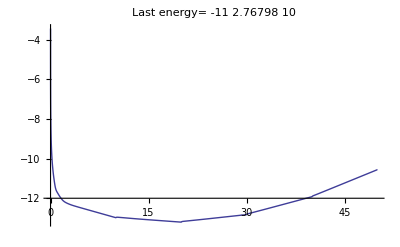

```mathematica
len=Transpose[Select[Import["energy(0.53).dat","Table"],(0<First[#])&]];
ltm=First[len];(*PrintRange[dif[ltm],All,PlotLabel->"Time step"]*)
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,mAx,mdAx,mAy,mdAy,mAz,mdAz,mBx,mBy,mBz,mqp,mqvx,mqvy,mqvz,mqAx,mqAy,mqAz,mqBx,mqBy,mqBz}=Transpose[{ltm,#}]&/@Drop[len,2];
(*PrintRange[{#⟦1⟧/3,#⟦2⟧}&/@(mqvx+mqvy+mqvz)]*)
(*PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqAx+mqAy+mqAz),All,PlotLabel->"Last energy="<>ToString[Last[Last[mqAx+mqAy+mqAz]]]]*)
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(mqBx+mqBy+mqBz),All,
PlotLabel->"Last energy="<>ToString[Last[Last[mqBx+mqBy+mqBz]]]]
```

```mathematica
HarmClearance[l_]:=Divide@@Take[Sort[Take[Abs@Fourier@l,Ceiling[Length[l]/2]]],-2]
```

```mathematica
out=.;ReadBinarySnapFiles["ponom_","_02282.snp",6,out,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,2},NumberOfRefs->4];
{Bx,By,Bz}=rotc[Sequence@@Take[out,-3],3];
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,14]]
-10Log[10,HarmClearance[WithoutFict@Bx⟦13,All,8⟧]]
```

5.61504

```mathematica
EstimateBoundary/@{Bx,By,Bz}
```

{63.4129,410.987,127.973}

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{{mqvx,mqvy,mqvz,mqp},{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]&/@{mqAx,mqAy,mqAz},{"Mean quadratic of Ar","Mean quadratic of Aϕ","Mean quadratic of Az"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]/2}],#]&/@{mdAx,mdAy,mdAz},{"Difference of Ar","Difference of Aϕ","Difference of Az"}}]
```

```mathematica
grs=MapThread[PrintRange[#1,Automatic+0{-1,1},PlotLabel->#2]&,{dif[Map[Function[l,{l⟦1⟧,Log[l⟦2⟧]/2}],#]]&/@{mqBx,mqBy,mqBz},{"Mean quadratic of Br","Mean quadratic of Bϕ","Mean quadratic of Bz"}}]
```

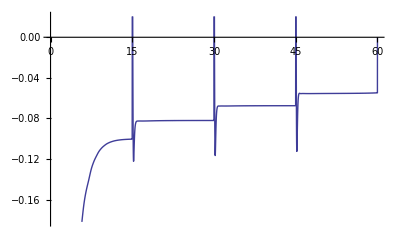

```mathematica
PrintRange[dif[{(#⟦1⟧)/3,Log[#⟦2⟧]/2}&/@(mqBx+mqBy+mqBz)],Automatic+0 0.2{-1,1}]
```

```mathematica
PrintRange[{#⟦1⟧10/0.5,#⟦2⟧}&/@dif[{(#⟦1⟧)/3,Log[#⟦2⟧]/2}&/@(mqBx+mqBy+mqBz)],0Automatic+0+0.1{-1,1}]
```

```mathematica
Interpolation[Reverse/@({{30,0.24},{32,0.278},{34,0.3072},{36,0.334},{38,0.358}}),InterpolationOrder->1][0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

17.3684

```mathematica
{0.5/10(ToExpression[#]),#}&/@cs[[1,2]]
```

{{1.,20.0000},{1.5,30.0000},{2.,40.0000},{2.5,50.0000},{3.,60.0000},{3.5,70.0000},{4.,80.0000},{4.5,90.0000},{5.,100.0000},{5.5,110.0000},{6.,120.0000},{6.5,130.0000},{7.,140.0000},{7.5,150.0000},{8.,160.0000},{8.5,170.0000},{9.,180.0000},{9.5,190.0000},{10.,200.0000},{10.5,210.0000},{11.,220.0000},{11.5,230.0000},{12.,240.0000},{12.5,250.0000}}

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[Abs[l⟦2⟧]]}],#]&/@{mAx,mAy,mAz},{"Maximum of Ar","Maximum of Aϕ","Maximum of Az"}}]
```

```mathematica
PrintRange[Select[mBy,Last[#]≠0&],Automatic]
```

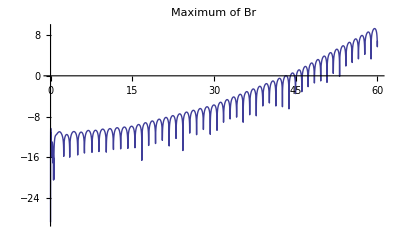
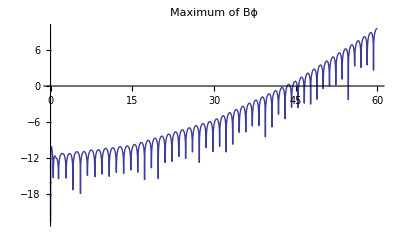
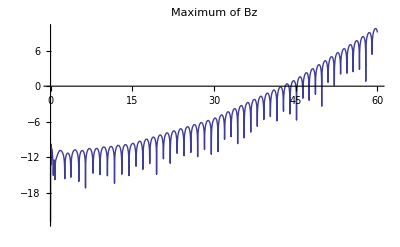

```mathematica
grs=MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[Function[l,{l⟦1⟧,Log[E,Abs[l⟦2⟧]]}],#]&/@{mBx,mBy,mBz},{"Maximum of Br","Maximum of Bϕ","Maximum of Bz"}}]
```

```mathematica
κ=0.50;
```

#### Чтение из файлов

```mathematica
Remove[PrintInfo]
```

```mathematica
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},NumberOfRefs->4];
```

```mathematica
out=.;ReadBinarySnapFile["screw.dmp",8,out,PrintInfo->Debug];
```

{1,1,2}

{0.,0,32,32,32,1000.}

Length of read from binary=508288 and size of it=2033152 bytes

ghost=3

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",4,out,PrintInfo->Debug];
```

{1,1,1}

{0.,0,64,64,64,3.14}

Length of read from binary=1372000 and size of it=5488000 bytes

ghost=3

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{4,4,1},NumberOfRefs->4];
```

```mathematica
{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0},ProcDistrib->{4,4,1},NumberOfRefs->4];
```

```mathematica
GetCoor[a_,b_,n_,ghost_]:=Block[{dx},
dx=(b-a)/n;
Table[a+i dx,{i,0.5-ghost,n+ghost-0.5,1}]
]
```

```mathematica
out=.;ReadBinarySnapFile["screw_512_17717.snp",6,out,PrintInfo->Debug];
(*{coor,bounds,node}=ReadAuxFiles3D[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{4,4,1},NumberOfRefs->3];
Print[bounds];*)
κ=0.80;
parR=3;parRfl=1;
coor=MapThread[GetCoor[#1,#2,#3,ghost]&,{{-(parR+parRfl/κ),-(parR+parRfl/κ),-parR},{(parR+parRfl/κ),(parR+parRfl/κ),parR},Rest[Dimensions[out]]-2ghost}];
bounds={#[[ghost]]+#[[ghost+1]],#[[-ghost]]+#[[-ghost-1]]}/2&/@coor
```

{8,16,4}

{25.0008,17717,128,128,64,26.}

Length of read from binary=20815872 and size of it=83263488 bytes

ghost=3

{{-4.25,4.25},{-4.25,4.25},{-3.,3.}}

```mathematica
If[Length[out]>6,out=Take[out,{2,-2}]];
```

```mathematica
out=.;ReadBinarySnapFiles["screw",".dmp",8,out,PrintInfo->None];
(*{vx,vy,vz,Ax,Ay,Az}=out;*)
{coor,bounds,node}=ReadAuxFiles3D[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{4,4,1},NumberOfRefs->0];
```

```mathematica
out=.;ReadBinarySnapFile["velocity.snp",5,out,PrintInfo->None];
```

Выделение внутренней области

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
GetVacuum[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(1-(node/.b_:>BitAnd[b,8])/8)#&/@Transpose[ar]],2,(1-(node/.b_:>BitAnd[b,8])/8)ar,_,$Failed]]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=GetInner/@{vx,vy,vz,p,nut};
```

```mathematica
{Bx,By,Bz}=rotd[Sequence@@Take[out,-3],3];
(*{jx,jy,jz}=rotd[Bx,By,Bz,3];*)
```

#### Проверка совпадения

```mathematica
{p1,vx1,vy1,vz1,Axm1,Aym1,Azm1,nutm1}={p,vx,vy,vz,Axm,Aym,Azm,nutm};
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}={p,vx,vy,vz,Ax,Ay,Az,nut};
```

```mathematica
{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}=out;
```

```mathematica
Max/@Abs[{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1}-{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2}]
```

{1.,1.5,1.,1.9,1.03193,1.0119,1.03194,1.}

```mathematica
out1=out;
```

```mathematica
{p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}={p,vx,vy,vz,Ax,Ay,Az,nut,Axm,Aym,Azm,nutm};
```

```mathematica
Max[Abs[#]]&/@({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}-{p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

{0.,0.,0.,0.,0.,0.,0.,0,0.,0.,0.,0.}

```mathematica
({p2,vx2,vy2,vz2,Ax2,Ay2,Az2,nut2,Axm2,Aym2,Azm2,nutm2}=={p1,vx1,vy1,vz1,Ax1,Ay1,Az1,nut1,Axm1,Aym1,Azm1,nutm1})
```

True

```mathematica
(*Brfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_fi Azi[r,fi,z]-∂_z Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bϕfi[r1_,fi1_,z1_]=ReplaceAll[∂_z Axi[r,fi,z]-∂_r Azi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[∂_r Ayi[r,fi,z]-1/r∂_fi Axi[r,fi,z]+1/r Ayi[r,fi,z],{r->r1,fi->fi1,z->z1}];
Bzfi[r1_,fi1_,z1_]=ReplaceAll[1/r∂_r (r Ayi[r,fi,z])-1/r∂_fi Axi[r,fi,z],{r->r1,fi->fi1,z->z1}];*)
```

#### Величины

```mathematica
EstimateBoundary[mat_?ArrayQ]:=Block[{Ein,Eb,ds=Dimensions[mat]},
(*Ein=Mean[Flatten@mat⟦2;;-2,All,2;;-2⟧^2];
Eb=√(((Times@@ds) Mean[Flatten@mat^2]-(Times@@(ds-2))Ein)/((Times@@ds)-(Times@@(ds-2))));
Eb/Max[Flatten@Abs@mat]*)
(Max@Abs@Flatten@mat⟦2;;-2,All,2;;-2⟧)/(Max@Abs@Complement[Flatten@mat,Flatten@mat⟦2;;-2,All,2;;-2⟧])
]
```

```mathematica
Max[Abs[Flatten[#]]]&/@(out1-out)
```

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Max@Abs@√Total[Take[out,{2,4}]^2]
```

1.59816

```mathematica
Total[Flatten[#^2]]&/@out
```

```mathematica
Max/@Abs@out
```

{1.49676,1.49676,1.86638,0.00500015,0.00499985,0.00499985}

```mathematica
√(Mean/@Flatten/@({Bx,By,Bz}^2))
```

{1.21144×10^10,4.3921×10^10,1.37365×10^10}

```mathematica
Mean/@Flatten/@{Bx,By,Bz}
```

{-2.04068×10^8,5.59908,-5.76753×10^8}

```mathematica
(√(Mean/@Flatten/@({Bx,By,Bz}^2)))/(Mean/@Flatten/@{Bx,By,Bz})
```

{-59.3645,7.84432×10^9,-23.817}

#### Простые графики

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,3,19]],PlotRange->All,DisplayFunction->Identity]&,
Take[out,4]]
```

```mathematica
Show2x[ListPlot3D[Transpose[GetVacuum[Cut3D[#,2,7]]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,p}]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,3,19]],PlotRange->All,DisplayFunction->Identity]&,{Bx,By,Bz,out[[1]]}]
```

```mathematica
Table[ListPlot3D[Transpose[Cut3D[Bz,2,i]],PlotRange->All,DisplayFunction->Identity],{i,36}]
```

```mathematica
ListPlot3D[Transpose[Cut3D[out⟦5⟧,2,7]],PlotRange->All,DisplayFunction->Identity]
```

```mathematica
PrintRange[out⟦2,23,All,23⟧]
```

```mathematica
Show2x[ListPlot3D[Cut3D[#,2,4],DisplayFunction->Identity,PlotRange->All]&,{Bx,By,Bz,Last[out]}]
```

```mathematica
(*Show4[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,√(vx^2+vy^2+vz^2)}];*)
Show2x[ListPlot3D[Transpose[Cut3D[#]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Ax,Ay,Az,nut}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{Bx,By,Bz,√(Bx^2+By^2+Bz^2)}]
Show2x[ListPlot3D[Transpose[Cut3D[WithoutFict[#]]],PlotRange->All,DisplayFunction->Identity,Mesh->False]&,{jx,jy,jz,√(jx^2+jy^2+jz^2)}]
```

```mathematica
dist=15;PrintRange[Cut3D[Cut3D[Bx,3,dist],1,dist]]
```

```mathematica
(*ListPlot3D[Transpose[Cut3D[Ay/coor⟦1⟧-PD[Ax,ghost,dx⟦2⟧,2]/coor⟦1⟧]]];
ListPlot3D[Transpose[Cut3D[PD[Ay,ghost,dx⟦1⟧,1]]]];*)
```

#### Интерполированные графики

```mathematica
{vxi,vyi,vzi,pi,Axi,Ayi,Azi,Bxi,Byi,Bzi,jxi,jyi,jzi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vx,vy,vz,p,Ax,Ay,Az,Bx,By,Bz,jx,jy,jz,nut};
```

```mathematica
Show[GraphicsRow[{SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,1.8],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧],AspectRatio->Automatic]},Spacings->Scaled[0.]],AspectRatio->1]
```

```mathematica
Show[GraphicsRow[{SectionRZ[jxi,jyi,jzi,0.3 π],SectionRΦ[jxi,jyi,jzi,Mean[bounds⟦3⟧]],SectionΦZ[jxi,jyi,jzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.]],AspectRatio->1,ImageSize->1000]
```

#### Оценки закрутки

```mathematica
{vx,vy,vz}=Take[out,{2,4}-1];
```

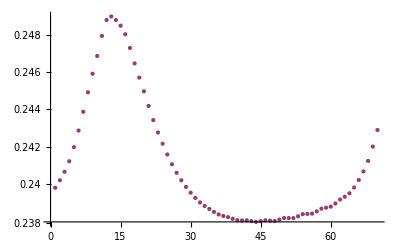

```mathematica
ListLogPlot[{Max/@Flatten/@Transpose[vx],√(Mean/@((Flatten/@Transpose[vz])^2))}]
```

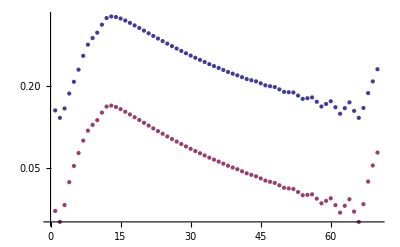

```mathematica
k
```

```mathematica
helicity=Total[MapThread[Times,{Take[out,3],rotd[Sequence@@Take[out,3],ghost]}]];
```

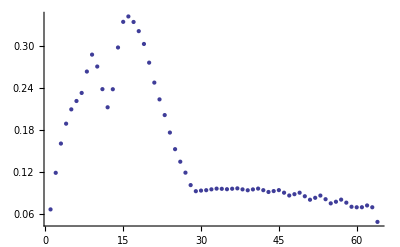

```mathematica
ListPlot[WithoutFict[Max/@Transpose[helicity]]]
```

```mathematica
phi=Outer[ArcTan,coor[[1]],coor[[3]]];
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];
vrho=Table[vx[[All,ny,All]]Cos[phi]+vz[[All,ny,All]]Sin[phi],{ny,Dimensions[vx][[2]]}];
```

```mathematica
PrintRange[Max/@Flatten/@Transpose[vy]]
```

```mathematica
Fit[Take[Transpose[{coor[[2]],Log/@Max/@Flatten/@vphi}],{10,19}],{1,z},z]
```

0.120886-0.0254404 z

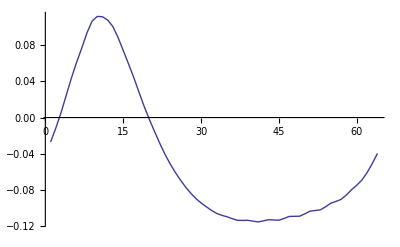

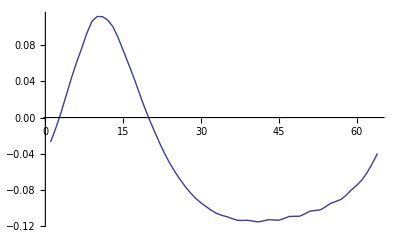

```mathematica
PrintRange[Log/@Max/@Flatten/@WithoutFict@vphi]
PrintRange[Log/@Max/@Flatten/@WithoutFict@vrho]
```

#### Графики сечений

Funcs

```mathematica
SectionΦ[vri_,vϕi_, vzi_,ϕ0_, opts___]:= Block[
	{func, funct, vmax, vmin, gr, coor=Global`coor, bounds=Global`bounds, 
		cf=ColorFunction/.{opts}/.{ColorFunction->"SunsetColors"},
		marg=SpaceMargin/.{opts}/.Options[SectionRZ],
		ar=AspectRatio/.{opts}/.Options[SectionRZ],
	rc=RadiusCurvature/.{opts}/.{RadiusCurvature->0},
		intervals,NormForm,
		r,ϕ,z
	},
bounds[[1]]={-0.1,3.5};
bounds[[3]]=2{-1,1};
intervals=-Apply[Subtract,#]&/@bounds;
	NormForm[n_]:=ToString[CForm[ACPackages`ACListNumerics`CutNumber[n]]];
	func=Function[{r, z}, vϕi[r Cos[ϕ0],r Sin[ϕ0], z]]; funct = Flatten[Outer[func, coor[[1]],coor[[3]]]];
	vmax = Max[funct]; vmin = Min[funct];
	func = Function[{r,z}, Sqrt[vzi[r Cos[ϕ0],r Sin[ϕ0],z]^2 + vri[r Cos[ϕ0],r Sin[ϕ0], z]^2]];
	funct = Flatten[Outer[func, coor[[1]], coor[[3]]]]; 
	vecmax = Max[funct];
	gr = Show[
		ContourPlot[vϕi[r Cos[ϕ0],r Sin[ϕ0], z], {r,bounds[[1,1]], bounds[[1,2]]}, {z, bounds[[3,1]], bounds[[3,2]]}, 
			PlotRange->All, DisplayFunction->Identity, ColorFunction->cf, ContourLines->False, Contours->20,PlotPoints->50
			],
		VectorPlot[{vri[r Cos[ϕ0],r Sin[ϕ0], z],vzi[r Cos[ϕ0],r Sin[ϕ0], z]},
			{r, bounds[[1,1]], bounds[[1,2]]}, 
			{z, bounds[[3,1]],bounds[[3,2]]},VectorScale->0.05,
			 Frame->False,VectorPoints-> 25,DisplayFunction->Identity
		],
		Graphics[Circle[{rc, Mean[bounds[[3]]]}, 1]],
  		Graphics[Arrow[{{0,bounds[[3,1]]},{0,bounds[[3,2]]}}]],
		AspectRatio->ar, 
		PlotRange -> MapThread[{#1[[1]]-marg #2,#1[[2]]+marg #2}&,Drop[#,{2}]&/@{bounds,intervals}]
	]
	(*ShowLegend[gr, {cf[1 - #] &, 10, NormForm[vmin], NormForm[vmax],
		LegendPosition->{-0.9, 1.1}, LegendOrientation->Horizontal, LegendSize->{1.9, 0.3},
		LegendTextOffset->{0,-1}, LegendLabel->("|vector|="<>NormForm[vecmax]),
		LegendBorderSpace ->0.2}, DisplayFunction->Identity
	]*)
]
```

```mathematica
DrawSectionDec[arrx_?ArrayQ, arry_?ArrayQ, arrz_?ArrayQ, opts___]:=Block[
		{xi,yi,zi,phi,Cphi,Sphi,(*Br,Bphi,*)
			ptsec=PointOfSections/.{opts}/.Options[DrawSection],
			ar=AspectRatio/.{opts}/.Options[DrawSection],
			cf=ColorFunction/.{opts}/.Options[DrawSection],
			pl=PlotLabel/.{opts}/.Options[DrawSection], pltext,
			os=OnlySection/.{opts}/.Options[DrawSection], grseq
		},
		(*phi=Outer[ArcTan[#1,#2]&,Global`coor[[1]],Global`coor[[2]]];*)phi=ptsec[[1]];
		Cphi=Cos[phi];Sphi=Sin[phi];
		{Br,Bphi}={arrx Cphi+arry Sphi,arry Cphi-arrx Sphi};
		{xi,yi,zi}=ListInterpolation[#,
			{{Min[Global`coor[[1]]],Max[Global`coor[[1]]]},
			{Min[Global`coor[[2]]],Max[Global`coor[[2]]]},
			{Min[Global`coor[[3]]],Max[Global`coor[[3]]]}
			},
			InterpolationOrder->1]&/@{Br,Bphi,arrz};
		grseq=SectionΦ[xi,yi,zi,ptsec[[1]],opts];
		grseq=If[!os,Join[{grseq},
			{SectionRΦ[xi,yi,zi,ptsec[[2]],ColorFunction->cf,AspectRatio->ar],
			SectionΦZ[xi,yi,zi,ptsec[[3]],ColorFunction->cf,AspectRatio->ar]}
			],
		{grseq}
		];
		pltext = Which[pl===None,"",
					Head[pl]===String,pl,
					pl===Automatic,("t="<>ToString[Global`tsec])
				];
		Return[If[os,First[grseq],GraphicsArray[grseq,AspectRatio->1,PlotLabel->pltext]]
			];
	]
```

```mathematica
DrawSection[Sequence@@Take[out,{2,4}-1],PointOfSections->{0.5,0,0}]
```

```mathematica
{Bxi,Byi,Bzi}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->3]&/@{Bx,By,Bz};
ϕmax=ϕ/.Last[Maximize[Bzi[Cos[ϕ]/κ,Sin[ϕ]/κ,0],ϕ]]
```

-0.596173

```mathematica
Manipulate[ListVectorPlot[Transpose[{WithoutFict[Bx][[All,All,i]],WithoutFict[By][[All,All,i]]},{3,1,2}]],{i,1,Last[Dimensions[Bx]]-2ghost,1}]
```

```mathematica
gr=DrawSectionDec[Bx,By,Bz,PointOfSections->{ϕmax+1 π/4,0,0},OnlySection->True,AspectRatio->Automatic,RadiusCurvature->1/κ,PlotLabel->None,ColorFunction->(ColorData["SunsetColors"][#]&)]
```

```mathematica
Export["final"<>ToString[κ]<>"sec1.gif",gr,ImageResolution->300,ImageSize->640]
```

final0.9sec1.gif

```mathematica
Export["final"<>ToString[κ]<>"sec1.gif",DrawSectionDec[Bx,By,Bz,PointOfSections->{ϕmax+0 π/2,0,0},OnlySection->True,AspectRatio->Automatic,RadiusCurvature->1/κ,PlotLabel->None],ImageResolution->300,ImageSize->640]Export["final"<>ToString[κ]<>"sec2.gif",DrawSectionDec[Bx,By,Bz,PointOfSections->{ϕmax+1 π/2,0,0},OnlySection->True,AspectRatio->Automatic,RadiusCurvature->1/κ,PlotLabel->None],ImageResolution->300,ImageSize->640]
```

final0.75909sec1.gif final0.75909sec2.gif

```mathematica
DrawSection[Transpose[Bx],Transpose[By],Transpose[Bz],PointOfSections->{0,0,0},OnlySection->False]
```

```mathematica
DrawSection[jx,jy,jz,PointOfSections->{0.5,0,0}]
```

```mathematica
PrintRange[WithoutFict@Bx⟦10,All,25⟧]
```

```mathematica
PrintRange[Take[Abs@Fourier@WithoutFict@Bx⟦15,All,15⟧,10]]
```

```mathematica
ReadDrawSection["dynamo_2_12820.snp",Binary,8,{5,6,7}]
```

```mathematica
DrawSection[Sequence@@ReadSection[4314]]
```

```mathematica
Table[ListPlot3D[Cut3D[Az,2,i],PlotRange->All],{i,1,Dimensions[By][[2]]}]
```

#### Чтение вдоль снэпов

```mathematica
Clear[ReadSection];
ReadSection[iter_,κ_Real,fluct_Symbol:False]:=Block[{dump,str=ToString[iter],Ax,Ay,Az,fname},
(*While[StringLength[str]<5,str="0"<>str];*)
(*dump=.;ReadBinarySnapFiles["dynamo_","_"<>str<>".snp",5,dump,PrintInfo->None];*)
fname="screw_512_"<>str<>".snp";
If[!FileExistsQ[fname],Return[$Failed{1,1,1}]];
dump=.;ReadBinarySnapFile[fname,6,dump,PrintInfo->None];
dump=Take[dump,{1,-1}];
(*Return[Take[dump,3]];*)
(*If[Head[coor]≠List,{coor,bounds}=ReadAuxFiles[{"coord"},ShiftVector->{0,0,0}]];*)
parR=2;parRfl=1;
coor=MapThread[GetCoor[#1,#2,#3,ghost]&,{{-(parR+parRfl/κ),-(parR+parRfl/κ),-parR},{(parR+parRfl/κ),(parR+parRfl/κ),parR},Rest[Dimensions[dump]]-2ghost}];
bounds={#[[ghost]]+#[[ghost+1]],#[[-ghost]]+#[[-ghost-1]]}/2&/@coor;
{Ax,Ay,Az}=Take[dump,-3];
{Bx,By,Bz}=rotd[Ax,Ay,Az,ghost];
(*{jx,jy,jz}=rotc[Bx,By,Bz,ghost];*)
Return[{Bx,By,Bz}];];
ReadSection[iter_,κ_Integer:0,fluct_Symbol:False]:=ReadSection[iter,κ+0.,fluct];
```

```mathematica
bounds
```

{{-4.31579,4.31579},{-4.31579,4.31579},{-3.,3.}}

```mathematica
grtot={};
```

```mathematica
nameexp="parker";
```

Независимый код

```mathematica
Block[{g,dump},dump=ReadList["runtest1.dmp"];np=dump⟦3⟧;KolProc=Times@@np;dump=Drop[dump,{3}];{t,count,n1,n2,n3,Rey}=Take[dump,6];dump=Drop[dump,6];{pm,vxm,vym,vzm,Axm,Aym,Azm,nutm}=Transpose[Partition[dump,8]];ghost=(Total[(Last[Dimensions[#1]]&)/@CutList[pm,Last[np]]]-n3)/(2 Last[np]);coor=ReadList["coord",Number,RecordLists->True];bounds=({1/2 (#1⟦ghost⟧+#1⟦ghost+1⟧),1/2 (#1⟦-ghost⟧+#1⟦-ghost-1⟧)}&)/@coor;Ax=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Axm,{1,2,3}]];Ay=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Aym,{1,2,3}]];Az=First[Fold[Map[Function[m,Clue[m,#2,ghost]],Partition[#1,np⟦#2⟧],{1}]&,Azm,{1,2,3}]];{Ax,Ay,Az}-=Transpose[Table[coor⟦1,i⟧ Cos[coor⟦2,j⟧] {Sin[coor⟦2,j⟧],Cos[coor⟦2,j⟧],0},{i,1,n1+2 ghost},{j,1,n2+2 ghost},{k,1,n3+2 ghost}],{2,3,4,1}];{Bx,By,Bz}=rotc[Ax,Ay,Az,ghost];{jx,jy,jz}=rotc[Bx,By,Bz,ghost];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=GraphicsRow[{SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]]},Spacings->Scaled[0.],PlotLabel->"t="<>ToString[t]];
fname=nameexp<>"0000.gif";
Export[fname,g,ImageResolution->300,ImageSize->640];]
```

```mathematica
ReadSectionDraw2File[iter_,κ_Real]:=Block[{fname},
{Bx,By,Bz}=ReadSection[iter,κ];
If[Bx===$Failed,Print["Failed in ",{iter,κ}];Return[$Failed]];
{Bxi,Byi,Bzi}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->3]&/@{Bx,By,Bz};
ϕmax=ϕ/.Last[Maximize[Bzi[Cos[ϕ]/κ,Sin[ϕ]/κ,0],ϕ]];
Export["section_"<>ToString[iter]<>"k"<>ToString[κ]<>"_sec1.gif",DrawSectionDec[Bx,By,Bz,PointOfSections->{ϕmax+0 π/2,0,0},OnlySection->True,AspectRatio->Automatic,RadiusCurvature->1/κ,PlotLabel->None],ImageResolution->300,ImageSize->640];Export["section_"<>ToString[iter]<>"k"<>ToString[κ]<>"_sec2.gif",DrawSectionDec[Bx,By,Bz,PointOfSections->{ϕmax+1 π/4,0,0},OnlySection->True,AspectRatio->Automatic,RadiusCurvature->1/κ,PlotLabel->None],ImageResolution->300,ImageSize->640];
phi=Outer[ArcTan[#1,#2]&,coor[[1]],coor[[2]]];
Bphi=(Bx Sin[phi]-By Cos[phi]);
val=WithoutFict[Sign[Bphi] √(By^2+Bx^2+Bz^2)];
mx = Max[Abs@val];
{min,max}=mx{-1,1};
gh= ListContourPlot3D[Transpose[val,{3,2,1}], Contours ->(min+max)/2+(max-min)/2 1/2.5{-1/2,1/2} ,ContourStyle -> {Directive[Yellow, Opacity[0.6]], Directive[Lighter[Blue], Opacity[0.6]]}, BoxRatios -> Automatic, Mesh -> False, AxesLabel -> {x, y, z}, DataRange -> bounds,ViewPoint->{1,-3,3}];
Export["surf"<>ToString[iter]<>"k"<>ToString[κ]<>".gif",Show[gh,gt[1/κ],sec[ϕmax],sec[ϕmax+π/2]],ImageResolution->300,ImageSize->640];
]
```

```mathematica
ReadSectionDraw2File[10199,0.45]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
```

{10199,10564,10866,11178,11468,14878,15263,20395,21119,21670,22249,26629,29628,30600,31679,32529,33314,38006,40691,40792,42214,43410,44425,45582}

```mathematica
nums=ToExpression[#⟦3,-1⟧&/@cs]
```

{27958,27555,27134,26790,26438,26134,25634,25277,24861,24441,24084,23529,23144,22712,22240,21732,17717}

```mathematica
ToExpression[Flatten[#⟦1⟧&/@cs]]
```

{0.8,0.78,0.76,0.74,0.72,0.7,0.68,0.66,0.64,0.62,0.6,0.58,0.56,0.54,0.52,0.5,0.48}

```mathematica
ReadSection[nums[[1]],1]//Dimensions
```

{3,38,38,38}

```mathematica
infos=ScanSnaps;
```

Сетка одинаковая: {128,128,64}

Деление на процессы одинаковое: {8,16,4}

Структура у всех одинаковая

```mathematica
infos[[1]]
```

```mathematica
PrintRange[Sort@infos[[All,3]]]
```

```mathematica
lf1=lf2=lf3=lf4=lf5={};
Monitor[Do[Block[{Bx,By,Bz,g1,g2,fname},
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
(*Print["have read ponom_"<>ToString[nums⟦i⟧]<>".snp"];*)
AppendTo[lf1,Fourier@WithoutFict@Bx⟦15,All,15⟧];
AppendTo[lf2,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bx,{2,1,3}])];
AppendTo[lf3,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@By,{2,1,3}])];AppendTo[lf4,Fourier@(Total[Flatten[#^2]]&/@Transpose[WithoutFict@Bz,{2,1,3}])];
],{i,1,Length[nums]}],nums⟦i⟧];
```

```mathematica
Manipulate[ListLogPlot[Take[Abs@lf1⟦i⟧,15],PlotRange->{10^-20,10^5},PlotLabel->infos[[i]]],{i,1,Length[nums],1}]
```

```mathematica
κs=PrependTo[ToExpression[Flatten[#⟦1⟧&/@cs]],0.45]
```

{0.45,0.475,0.5,0.525,0.55}

```mathematica
cs[[1,1]]={0.45}
```

{0.45}

```mathematica
Monitor[Do[Block[{},
ReadSectionDraw2File[cs⟦j,-1,i⟧,cs⟦j,1,1⟧];
Print["have read κ="<>ToString[cs⟦j,1,1⟧]<>", iter="<>ToString[cs⟦j,-1,i⟧]<>".snp"];
(*g1=DrawSection[Bx,By,Bz];
fname="screw"<>ToString[nums⟦i⟧]<>"_B.gif";
Export[fname,g1,ImageResolution->300,ImageSize->640];*)
(*g2=DrawSection[jx,jy,jz];
fname="ponom"<>ToString[nums⟦i⟧]<>"_j.gif";
Export[fname,g2,ImageResolution->300,ImageSize->640];*)
],{j,1,Length[cs]},{i,1,Length[cs⟦j,-1⟧]}],{i,j}];
```

Failed in {3452,0.45}

have read κ=0.45, iter=3452.snp

Failed in {6825,0.45}

have read κ=0.45, iter=6825.snp

have read κ=0.45, iter=10199.snp

Failed in {13589,0.45}

have read κ=0.45, iter=13589.snp

Failed in {16992,0.45}

have read κ=0.45, iter=16992.snp

have read κ=0.45, iter=20395.snp

Failed in {23807,0.45}

have read κ=0.45, iter=23807.snp

Failed in {27207,0.45}

have read κ=0.45, iter=27207.snp

have read κ=0.45, iter=30600.snp

Failed in {33999,0.45}

have read κ=0.45, iter=33999.snp

Failed in {37391,0.45}

have read κ=0.45, iter=37391.snp

have read κ=0.45, iter=40792.snp

have read κ=0.4750, iter=3564.snp

have read κ=0.4750, iter=7068.snp

have read κ=0.4750, iter=10564.snp

have read κ=0.4750, iter=14070.snp

have read κ=0.4750, iter=17584.snp

have read κ=0.4750, iter=21119.snp

have read κ=0.4750, iter=24631.snp

have read κ=0.4750, iter=28155.snp

have read κ=0.4750, iter=31679.snp

have read κ=0.4750, iter=35192.snp

have read κ=0.4750, iter=38704.snp

have read κ=0.4750, iter=42214.snp

have read κ=0.5000, iter=3680.snp

have read κ=0.5000, iter=7274.snp

have read κ=0.5000, iter=10866.snp

have read κ=0.5000, iter=14466.snp

have read κ=0.5000, iter=18071.snp

have read κ=0.5000, iter=21670.snp

have read κ=0.5000, iter=25272.snp

have read κ=0.5000, iter=28893.snp

have read κ=0.5000, iter=32529.snp

have read κ=0.5000, iter=36157.snp

have read κ=0.5000, iter=39777.snp

have read κ=0.5000, iter=43410.snp

have read κ=0.5250, iter=3783.snp

have read κ=0.5250, iter=7479.snp

have read κ=0.5250, iter=11178.snp

have read κ=0.5250, iter=14878.snp

have read κ=0.5250, iter=18567.snp

have read κ=0.5250, iter=22249.snp

have read κ=0.5250, iter=25943.snp

have read κ=0.5250, iter=29628.snp

have read κ=0.5250, iter=33314.snp

have read κ=0.5250, iter=37001.snp

have read κ=0.5250, iter=40691.snp

have read κ=0.5250, iter=44425.snp

have read κ=0.5500, iter=3872.snp

have read κ=0.5500, iter=7668.snp

have read κ=0.5500, iter=11468.snp

have read κ=0.5500, iter=15263.snp

have read κ=0.5500, iter=19053.snp

have read κ=0.5500, iter=22843.snp

have read κ=0.5500, iter=26629.snp

have read κ=0.5500, iter=30420.snp

have read κ=0.5500, iter=34208.snp

have read κ=0.5500, iter=38006.snp

have read κ=0.5500, iter=41789.snp

have read κ=0.5500, iter=45582.snp

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
Dimensions[res]
```

{400,3,38,38,38}

```mathematica
Do[Block[{g},
temp=First[Import["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp.ZIP",{"*.snp","Binary"}]];
Export["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp",temp,"Binary","DataFormat"-> "Byte"];
{Bx,By,Bz}=ReadSection[nums⟦i⟧];
Print["have read dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
Close["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
DeleteFile["dynamo_2_"<>ToString[nums⟦i⟧]<>".snp"];
(*{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};g=DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity,PlotLabel->"t="<>ToString[t]];*)
g=DrawSection[Bx,By,Bz];
fname="dynamo"<>ToString[nums⟦i⟧]<>".gif";Export[fname,g,ImageResolution->300,ImageSize->640];],{i,1,Length[nums]}];
```

```mathematica
gr=Table[{Bx,By,Bz,jx,jy,jz}=ReadSection[i];{Bxi,Byi,Bzi,jxi,jyi,jzi}=(ListInterpolation[#1,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&)/@{Bx,By,Bz,jx,jy,jz};DisplayTogetherArray[SectionRZ[Bxi,Byi,Bzi,0.2 π],SectionRΦ[Bxi,Byi,Bzi,Mean[bounds⟦3⟧]],SectionΦZ[Bxi,Byi,Bzi,Mean[bounds⟦1⟧]],Spacings->Scaled[0.],DisplayFunction->Identity],{i,10,2820,10}];
```

```mathematica
grtot=First/@gr
```

```mathematica
Export["current.gif",Show[#,DisplayFunction->Identity]&/@gr,ConversionOptions->{"AnimationDisplayTime"->0.2},ImageResolution->300,ImageSize->640];
```

#### Сложное рисование поверхностей

```mathematica
{cont1, cont2} = (0.1*{Max[#1], Min[#1]} & )[By]
```

```mathematica
bounds
```

```mathematica
cubic=Table[Block[{r=√(x^2+y^2),f=ArcTan[y,x+10^-10]+π},If[z≤bounds⟦3,2⟧∧z≥bounds⟦3,1⟧∧r≤bounds⟦1,2⟧∧r≥bounds⟦1,1⟧,Byi[r,f,z],0]],{z,-1.5,1.5,0.2},{x,-6,6,0.2},{y,-6,6,0.2}];
```

```mathematica
g1 = ColorLighting[ListContourPlot3D[cubic, Contours -> {cont1}, DisplayFunction -> Identity], {1, 0, 0}];
g2 = ColorLighting[ListContourPlot3D[cubic, Contours -> {cont2}, DisplayFunction -> Identity], {0, 0, 1}];
```

```mathematica
Show[g1, Lighting -> Automatic]
```

```mathematica
Show[Graphics3D[EdgeForm[]], g1, g2, Lighting -> None]
```

```mathematica
Show[Graphics3D[EdgeForm[]], ColorLighting[ListContourPlot3D[cubic, Contours -> {cont1}, DisplayFunction -> Identity], {1, 0, 0}], ColorLighting[ListContourPlot3D[cubic, Contours -> {cont2}, DisplayFunction -> Identity], {0, 0, 1}], Lighting -> None]
```

#### Простое рисование поверхностей

```mathematica
{min,max}={Max[#],Min[#]}&@helicity
```

{1.83789,-0.0597603}

```mathematica
val=WithoutFict[√(By^2+Bx^2+Bz^2)];
mx = Max[Abs@val]
{min,max}=mx{-1,1};
```

0.0000107805

```mathematica
val=out[[2]];
mx = Max[Abs@val]
{min,max}={0,mx};
```

1.49676

```mathematica
val=WithoutFict[Bz];
mx = Max[Abs@val]
{min,max}=mx{-1,1};
```

0.000370324

```mathematica
phi=Outer[ArcTan[#1,#2]&,coor[[1]],coor[[2]]];
Bphi=(Bx Sin[phi]-By Cos[phi]);
val=WithoutFict[Sign[Bphi] √(By^2+Bx^2+Bz^2)];
mx = Max[Abs@val]
{min,max}=mx{-1,1};
```

1.60919×10^10

```mathematica
Bpol=√((By Sin[phi]+Bx Cos[phi])^2+Bz^2);
Bphi=(Bx Sin[phi]-By Cos[phi]);
```

```mathematica
val1=WithoutFict[Bphi];
mx1= Max[Abs@val1]
{min1,max1}=mx1{-1,1};
```

0.00171815

```mathematica
val1=WithoutFict[By Sin[phi]+Bx Cos[phi]];
mx1= Max[Abs@val1]
{min1,max1}=mx1{-1,1};
```

0.782711

```mathematica
gh= ListContourPlot3D[Transpose[val,{3,2,1}], Contours ->(min+max)/2+(max-min)/2 1/2.5{-1/2,1/2} ,ContourStyle -> {Directive[Yellow, Opacity[0.6]], Directive[Lighter[Blue], Opacity[0.6]]}, BoxRatios -> Automatic, Mesh -> False, AxesLabel -> {x, y, z}, DataRange -> bounds,ViewPoint->{1,-3,3}];
```

```mathematica
gt[r_]:=ParametricPlot3D[{(r+Cos[v]) Cos[u],(r+Cos[v]) Sin[u],Sin[v]},{u,0,2π},{v,0,2π},Mesh->False,PlotStyle->Directive[Opacity[0.9]]]
```

```mathematica
sec[ϕ_]:=With[{size=1.5},Graphics3D[{Green,Opacity[0.5],Polygon[{{(1/κ-size)Cos[ϕ],(1/κ-size)Sin[ϕ],-size},{(1/κ+size)Cos[ϕ],(1/κ+size)Sin[ϕ],-size},{(1/κ+size)Cos[ϕ],(1/κ+size)Sin[ϕ],size},{(1/κ-size)Cos[ϕ],(1/κ-size)Sin[ϕ],size}}]}]]
```

```mathematica
Show[gh,gt[1/κ],sec[ϕmax],sec[ϕmax+π/2]]
```

```mathematica
Export["final"<>ToString[κ]<>"surf.gif",gh,ImageResolution->300,ImageSize->640]
```

final0.75909surf.gif

```mathematica
gh1= ListContourPlot3D[Transpose[val1,{3,2,1}], Contours ->(min1+max1)/2+(max1-min1)/2 1/2{-1/2,1/2} , ContourStyle -> {Directive[Yellow, Opacity[0.8]], Directive[Pink, Opacity[0.8]]}, BoxRatios -> Automatic, Mesh -> False, AxesLabel -> {x, y, z}, DataRange -> bounds,ViewPoint->{0,0,∞}]
```

```mathematica
val2=WithoutFict[(Bx Sin[phi]-By Cos[phi])];
mx2 = Max[Abs@val2]
{min2,max2}=mx2{-1,1};
```

0.000193945

```mathematica
{Bxi,Byi,Bzi}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->3]&/@{Bx,By,Bz};
```

```mathematica
Plot[Bzi[Cos[ϕ],Sin[ϕ],1] ,{z,-2,2},Frame->True]
```

```mathematica
Plot[Byi[Cos[ϕ],Sin[ϕ],1] Sin[ϕ]+Bxi[Cos[ϕ],Sin[ϕ],1] Cos[ϕ] ,{ϕ,0,2π},Frame->True]
```

```mathematica
{Bx,By,Bz}={Bx,By,Bz}/Max[√(Bx^2+By^2+Bz^2)];
```

```mathematica
nds=First@NDSolve[{x'[t]==Bxi[x[t],y[t],z[t]],y'[t]==Byi[x[t],y[t],z[t]],z'[t]==Bzi[x[t],y[t],z[t]],x[0]==0,y[0]==0,z[0]==0},{x,y,z},{t,0,200}];
```

```mathematica
nds2=First@NDSolve[{x'[t]==-Bxi[x[t],y[t],z[t]],y'[t]==-Byi[x[t],y[t],z[t]],z'[t]==-Bzi[x[t],y[t],z[t]],x[0]==0,y[0]==0,z[0]==0},{x,y,z},{t,0,200}];
```

```mathematica
{x[t],y[t],z[t]}/.{nds,nds2}
```

{{InterpolatingFunction[{{0.,200.}},<>][t],InterpolatingFunction[{{0.,200.}},<>][t],InterpolatingFunction[{{0.,200.}},<>][t]},{InterpolatingFunction[{{0.,200.}},<>][t],InterpolatingFunction[{{0.,200.}},<>][t],InterpolatingFunction[{{0.,200.}},<>][t]}}

```mathematica
ParametricPlot3D[{x[t],y[t],z[t]}/.{nds,nds2},{t,0,200},AxesLabel->{x,y,z},PlotStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
gh2= ListContourPlot3D[Transpose[val2,{3,2,1}], Contours ->(min2+max2)/2+(max2-min2)/2 1/1.2{-1/2,1/2} , ContourStyle -> {Directive[Yellow, Opacity[0.8]], Directive[Pink, Opacity[0.8]]}, BoxRatios -> Automatic, Mesh -> False, AxesLabel -> {x, y, z}, DataRange -> bounds,ViewPoint->{0,0,∞}]
```

```mathematica
{gh1,gh2}
```

```mathematica
Export["final1.00.gif",,ImageResolution->300,ImageSize->640]
```

final1.00.gif

#### Просмотр массива типа ячеек и отражений

```mathematica
{node,ref} = ReadAuxFiles3D[{"node","ref"},NumberOfRefs->3,ProcDistrib->{4,4,1}];Dimensions[node]
```

{70,70,38}

```mathematica
nm=ReadList["node"];Dimensions[nm]
```

{8,38,22,38}

```mathematica
Union[Flatten[node]]
```

{36,40,68,72}

```mathematica
ArrayPlot[Transpose[Map[BitAnd[Round[#1], 31] &, node, {2}]], FrameTicks -> True, Mesh -> True, Frame -> True]
```

```mathematica
flag = 8 + 64;
ListDensityPlot[Transpose[Map[BitAnd[Round[#1], flag] &, nm[[2]], {2}]]]
ListDensityPlot[Transpose[Map[BitAnd[Round[#1], flag] &, nm[[1]], {2}]]]
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost,n1/2+ghost},n1/2]]
```

```mathematica
ListContourPlot3D[BitAnd[Round[node],32],Contours->10,PlotRange->All]
```

```mathematica
ListContourPlot3D[ref[[3]],PlotRange->All]
```

```mathematica
DisplayTogether[ListContourPlot[node], gc];
```